# Example 1 - Plotting the band-structure with BandUtilities

Anirudh Chandrasekaran

22 April 2024

## Loading the Library

We first load the library by executing the following:

```mathematica
AppendTo[$Path,StringDelete[NotebookDirectory[],"/Examples"]];
<<BandUtilities`
```

When using the library for other notebooks, copy the folder “Package” on to the folder containing the notebook and add and execute the following lines instead to load the library:

AppendTo[$Path,NotebookDirectory[]<>”Package”];
<<BandUtilities`

## A simple tight - binding model

We use the Haldane model since it is simple yet quite rich. The a_i are nearest neighbour lattice vectors while b_i are the nest nearest neighbour lattice vectors. We include a real nearest neighbour hopping t_1 and an imaginary next nearest neighbour hopping t_2 on the Honeycomb lattice. A staggered chemical potential μ is also included. K_1 and K_2 are the two K points that become inequivalent. We first define the parameters of the model:

```mathematica
(*Nearest neighbour vectors*)
a1={1,0};
a2={-1/2,(√3)/2};
a3={-1/2,(-√3)/2};

(*next nearest neighbour vectors*)
b1=a2-a3;
b2=a3-a1;
b3=a1-a2;

(*The two inequivalent K points*)
K1=(4π)/(3 √3){(√3)/2,1/2};
K2=(4π)/(3 √3){(√3)/2,-1/2};

(*One of the M points*)
Mp=(4π)/(3 √3){(√3)/2,0};
```

We proceed to define the Hamiltonian and its parts:

```mathematica
(*Nearest neighbour hopping terms*)
h1[k_]:=(ⅇ^(ⅈ k.a1)+ⅇ^(ⅈ k.a2)+ⅇ^(ⅈ k.a3));
HamltnNN[k_,t1_]:={{0,t1 h1[k]},{t1 Conjugate[h1[k]],0}};

(*Next nearest neighbour hopping terms*)
h2[k_]:=2(Sin[k.b1]+Sin[k.b2]+Sin[k.b3]);

σz=PauliMatrix[3];

(*Full Hamiltonian, including staggered chemical potential*)
HamltnFull[k_,t1_,t2_,μ_]:=HamltnNN[k,t1]+μ σz+t2 h2[k] σz;
```

## Plotting the Band structure for different cases

### Defining the paths in the Brillouin zone

We define two different paths in the k-space, one a continuous path and the other comprising of two continuous paths which are disconnected:

```mathematica
Path1={{{0,0},"Γ"},{K1,"K"},{Mp,"M"},{K2,"K'"},{{0,0},"Γ"}};
Path2={{{{0,0},"Γ"},{K1,"K"},{Mp,"M"},{{0,0},"Γ"}},{{Mp,"M"},{K2,"K'"},{{0,0},"Γ"}}};
```

### Case 1: Vanishing next nearest hopping and staggered chemical potential (graphene like model)

This model is the simplest case and we expect its band structure to be similar to that of graphene:

```mathematica
Hamltn1[k_]:=HamltnFull[k,1,0,0]

BandData1a=GenerateBandStructure[Hamltn1,Path1];
BandData1b=GenerateBandStructure[Hamltn1,Path2];
```

#### Along the continuous path

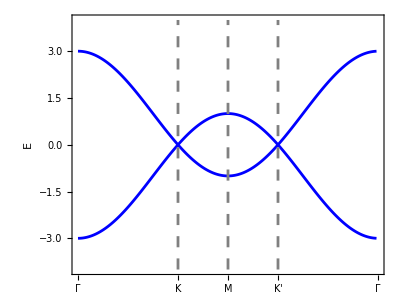

```mathematica
PlotBandStructure[BandData1a,{-4,4}(*y-range*)]
```

#### Along the piece-wise continuous path

The GenerateBandStructure routine automatically figures out if the path is continuous or broken and adjusts the generated data accordingly.

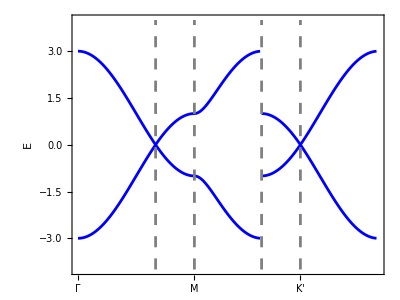

```mathematica
PlotBandStructure[BandData1b,{-4,4}(*y-range*)]
```

### Customising the Plot

We can customise the plots to a significant extent. We illustrate all the features now.

#### Changing label fonts

We can change the font size, colour and family for the y and x labels. Additionally the new y label must also be specified:

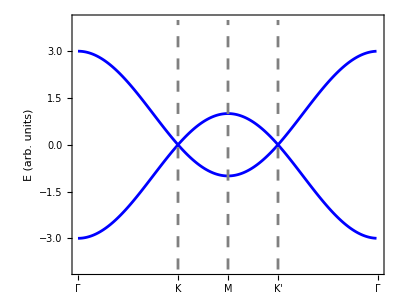

```mathematica
PlotBandStructure[BandData1a,{-4,4},"yLabel"->{"E (arb. units)",12,Black,"Times"},"xLabel"->{14,Gray,"Times"}]
```

We can also rotate the y-label:

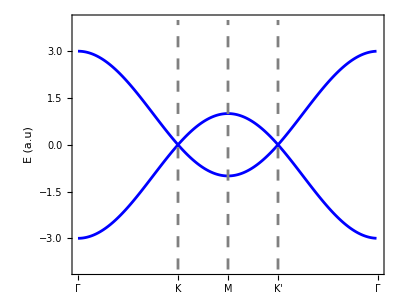

```mathematica
PlotBandStructure[BandData1a,{-4,4},"yLabel"->{"E (a.u)",12,Gray,"Helvetica"},"yLabelRotate"->-π/2(*theta in radians*)]
```

#### Changing the ticks

```mathematica
PlotBandStructure[BandData1a,{-4,4},"yTicks"->{16,Gray,"Courier"}]
```

-Graphics-

#### Changing the aspect ratio and setting various line properties

We can specify a list of colours. The routine will cycle through the colours for the different bands (here the band numbers are defined by simply ordering the eigenvalues at each k point). If we allow for orbital projections (see below) then the colours will be used for the orbitals.

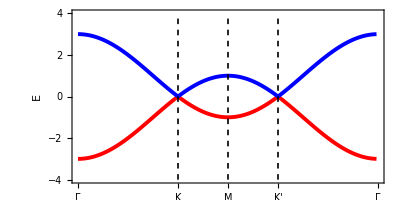

```mathematica
PlotBandStructure[BandData1a,{-4,4},"AspectRatio"->0.5,"LineThickness"->0.007,"LineColorScheme"->{Red,Blue},"DividingLines"->{0.01,Black,0.003}]
```

#### Including a legend

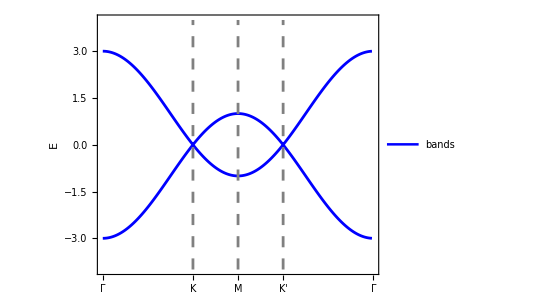

```mathematica
PlotBandStructure[BandData1a,{-4,4},"PlotKeyLegend"->{"bands",{0.75,0.93}}]
```

It is best to apply font effects on the legend while feeding it to the routine:

```mathematica
PlotBandStructure[BandData1a,{-4,4},"PlotKeyLegend"->{Style["bands",Gray,FontFamily->"Times New Roman"],{0.75,0.93}}]
```

-Graphics-

We will use the legends to encode information about the orbitals below, when we discuss orbital projections.

## Overlaying the band-structure of a set of models

We will illustrate how we can overlay a set of plots to track the evolution of the band structure. We will begin by choosing a colour scheme

```mathematica
ColourChoice={67/255,49/255,12/255};
OpacityList={0.3,0.5,0.75,1};
BlendingList=OpacityList;

HopParamList={{1,0,0},{1,1/8,0},{1,1/4,0},{1,1/4,1/8}};(*Each element is of the form {Subscript[t, 1],Subscript[t, 2],μ}*)
```

We can then generate a list of plot data that can be used to generate the figure

```mathematica
BandDataList1=First@Last@Reap[Do[
HamCurr[k_]:=HamltnFull[k,hops[[1]],hops[[2]],hops[[3]]];

Sow[GenerateBandStructure[HamCurr,Path1]];
,{hops,HopParamList}]];
```

The plot:

```mathematica
BandPlotList1=First@Last@Reap[Do[
Sow[PlotBandStructure[BandDataList1[[i]],{-4,3.5},"LineThickness"->0.004,"LineColorScheme"->{RGBColor[ColourChoice[[1]],ColourChoice[[2]],ColourChoice[[3]],OpacityList[[i]]]},"PlotKeyLegend"->{Style["t_2="<>ToString[Chop[HopParamList[[i,2]]//N]]<>", μ="<>ToString[Chop[HopParamList[[i,3]]//N]],FontSize->8],{0.35,0.25-i/20.}}]]
,{i,1,Length[HopParamList]}]];
```

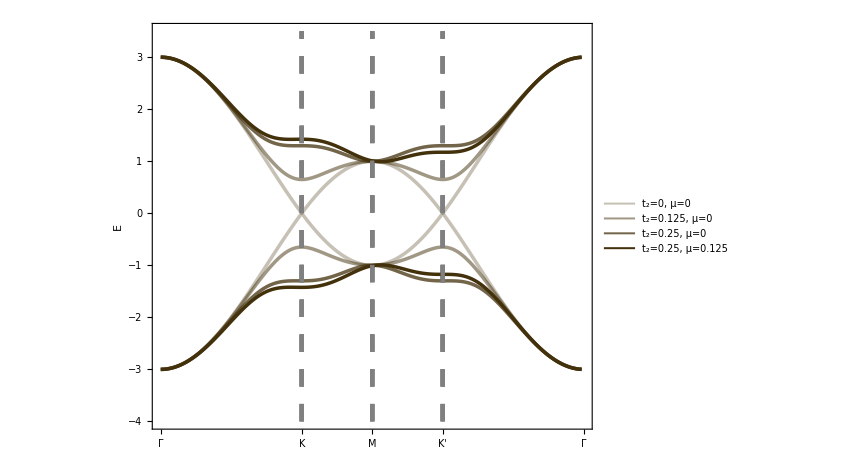

```mathematica
Show[BandPlotList1]
```

To save the graphics, just right click and choose “Save Graphics As”. In the options, choose “Highest Quality Vector Graphics” for both the options.

Sometimes, Mathematica runs into issues with transparent lines in ListLinePlot wherein it double plots some small line segments. In those situations, it might be better to use Blend function (with White) instead of RGBA colours as shown below

```mathematica
BandPlotList2=First@Last@Reap[Do[
Sow[PlotBandStructure[BandDataList1[[i]],{-4,3.5},"LineThickness"->0.004,"LineColorScheme"->{Blend[{White,RGBColor[ColourChoice[[1]],ColourChoice[[2]],ColourChoice[[3]]]},OpacityList[[i]]]},"PlotKeyLegend"->{Style["t_2="<>ToString[Chop[HopParamList[[i,2]]//N]]<>", μ="<>ToString[Chop[HopParamList[[i,3]]//N]],FontSize->8],{0.35,0.25-i/20.}}]]
,{i,1,Length[HopParamList]}]];
```

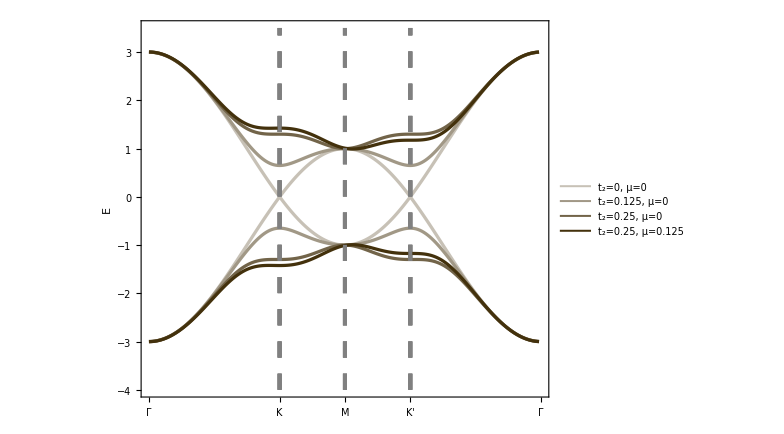

```mathematica
Show[BandPlotList2]
```

It essentially produces the same result as far as the eye can tell.

## Orbital Projections

For illustrating the orbital projections, let us define the following simple three band 1D tight binding model

```mathematica
Hamltn[{k_}]:={{1/4 Cos[k],1+Cos[k]-ⅈ Sin[k],1/8(1+Cos[k]-ⅈ Sin[k])},{1+Cos[k]+ⅈ Sin[k],1/4 Cos[k],1/8(1+Cos[k]-ⅈ Sin[k])},{1/8(1+Cos[k]+ⅈ Sin[k]),1/8(1+Cos[k]+ⅈ Sin[k]),3/2}}
```

The band structure is first generated with the option “OrbitalProjection” set to True

```mathematica
bds1=GenerateBandStructure[Hamltn,{{{0},"0"},{{π},"π"},{{2π},"2π"}},"OrbitalProjection"->True];
```

When plotting this, we can feed a legend and a colour scheme

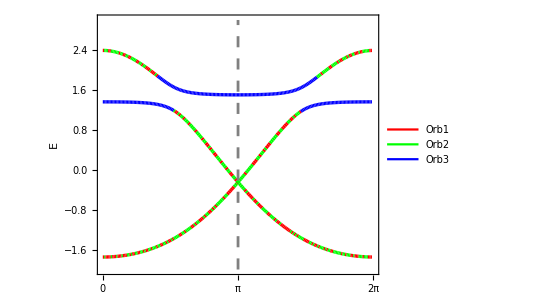

```mathematica
PlotBandStructure[bds1,{-2,3},"LineColorScheme"->{Red,Green,Blue},"PlotKeyLegend"->{{"Orb1","Orb2","Orb3"},{0.75,0.45}},"LineThickness"->0.006]
```

We can also look at the projections to groups of orbitals using the option “OrbitalGrouping”. If no legend (or an invalid legend) is provided, then it will use the indices of the orbital groups

```mathematica
bds2=GenerateBandStructure[Hamltn,{{{{0},"0"},{{π},"π"}},{{{-π/2},"-π/2"},{{π/2},"π/2"}}},"OrbitalProjection"->True,"OrbitalGrouping"->{{1,2},3}];
```

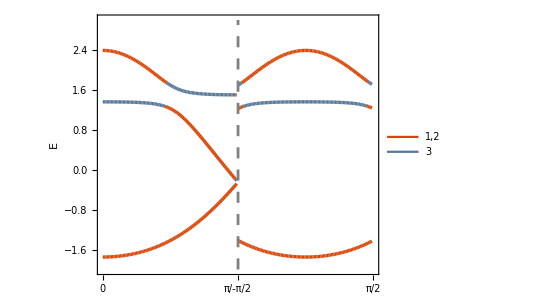

```mathematica
PlotBandStructure[bds2,{-2,3},"LineColorScheme"->{Red,Green,Blue},"PlotKeyLegend"->{{"Orb1","Orb2","Orb3"},{0.75,0.45}},"LineThickness"->0.006]
```

Here we had provided an invalid legend since there are only two groups and we provided three. So it automatically reverts to the orbital indices for the legend. If we don’t provide a valid colour scheme, it will choose a random set of colours

```mathematica
bds3=GenerateBandStructure[Hamltn,{{{{0},"0"},{{π},"π"}},{{{-π/2},"-π/2"},{{π/2},"π/2"}}},"OrbitalProjection"->True];
```

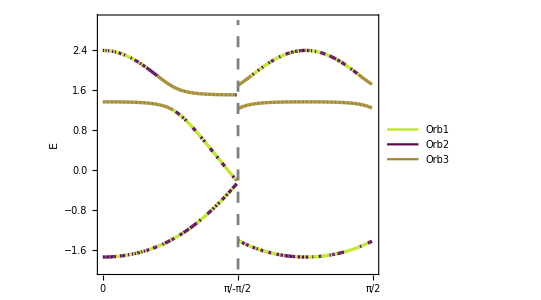

```mathematica
PlotBandStructure[bds3,{-2,3},"LineColorScheme"->{Red,Blue},"PlotKeyLegend"->{{"Orb1","Orb2","Orb3"},{0.75,0.45}},"LineThickness"->0.006]
```

Here again we provided an invalid option, namely a list of two colours for projection onto three orbitals.